```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
Forcing[x_,y_]:=Block[{},
0
]
```

```mathematica
(*Calcula os pontos e os pesos da regra de integração *)
IntegrationRule[order_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},
vecPtosPesos=Transpose[GaussianQuadratureWeights[2order+1,-1,1]];

pts=vecPtosPesos[[1]];
w=vecPtosPesos[[2]];
matpsts=Table[{pts[[j]],pts[[i]],w[[j]] w[[i]] },{i,Length[pts],1,-1},{j,1,Length[pts]}];
matpsts
]
```

```mathematica
(*Calcula os pontos e os pesos da regra de integração *)
IntegrationRule[order_,eltype_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},

If[eltype==1,
If[order==1,
matpsts={{-0.5773502691896257,0.5773502691896257,1.},{0.5773502691896257,0.5773502691896257,1.},{-0.5773502691896257,-0.5773502691896257,1.},{0.5773502691896257,-0.5773502691896257,1.}};
];
If[order==2,
matpsts={{-0.7745966692414834,0.7745966692414834,0.30864197530864174},{0.,0.7745966692414834,0.4938271604938271},{0.7745966692414834,0.7745966692414834,0.30864197530864174},{-0.7745966692414834,0.,0.4938271604938271},{0.,0.,0.7901234567901237},{0.7745966692414834,0.,0.4938271604938271},{-0.7745966692414834,-0.7745966692414834,0.30864197530864174},{0.,-0.7745966692414834,0.4938271604938271},{0.7745966692414834,-0.7745966692414834,0.30864197530864174}};
];

,
If[order==1,
matpsts={{1/3,1/3,1}};
];
If[order==2,
matpsts={{1/6,1/6,1/3},{2/3,1/6,1/3},{1/6,2/3,1/3}};
];

If[order==3,
matpsts={{1/3,1/3,-27/48},{1/5,1/5,25/48},{1/5,3/5,25/48},{3/5,1/5,25/48}};
];

];
matpsts//N
]
```

```mathematica
(*Dada a matriz de rigidez e o vetor de carga globais, aplica condição de contorno definida em nós*)
ApplyNodeBC[Kglob_,Fglob_,node_,type_,ek_,ef_]:=Block[{position,i,j,kglob=Kglob,fglob=Fglob},

If[type≠0&&type≠1 && type≠2,Print["Unknown type. Specify 0 for Dirichlet, 1 for Newman or 2 for Mixed."]];
position=node 2-1;
If[type==0,
(*Dirichlet - Specified Solution *)
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
kglob[[position+i-1,position+j-1]]*=ek[[i,j]];
];
fglob[[position+i-1]]=ef[[i]];
];
];
If[type==1,
For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];
];
];
{kglob,fglob}
]
```

```mathematica
Compute2DShape[order_,eltype_]:=Block[{ζ1,ζ2,ζ3,a,b,xi,eta,psis},

If[eltype==1,
(*Quad*)
If[order==1,

psis={0.25(1-xi)(1-eta),0.25(1+xi)(1-eta),0.25 (1+xi)(1+eta),0.25(1-xi)(1+eta)};
];
If[order==2,

psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
];

];

If[eltype==2,
ζ1=1-xi-eta;
ζ2=xi;
ζ3=eta;

If[order==1,
psis={ζ1,
ζ2, 
ζ3};

];
If[order==2,
psis={2*ζ1*(ζ1-1/2),
2*ζ2*(ζ2-1/2),
2*ζ3*(ζ3-1/2),
4*ζ1*ζ2,
4*ζ2*ζ3,
4*ζ3*ζ1};

];
If[order==3,
psis={(9/2)*ζ1*(ζ1-2/3)*(ζ1-1/3),
(9/2)*ζ2*(ζ2-2/3)*(ζ2-1/3),
(9/2)*ζ3*(ζ3-2/3)*(ζ3-1/3),
(27/2)*ζ1*ζ2*(ζ1-1/3),
(27/2)*ζ1*ζ2*(ζ2-1/3),
(27/2)*ζ2*ζ3*(ζ2-1/3),
(27/2)*ζ2*ζ3*(ζ3-1/3),
(27/2)*ζ3*ζ1*(ζ3-1/3),
(27/2)*ζ3*ζ1*(ζ1-1/3),
27*ζ1*ζ2*ζ3};

];
];
N[psis]
];
```

```mathematica
(*Calcula as funções psi as coordenas x e y, o gradiente de psi e o jacobiano *)
(*AQUI MUNDANCAS PARA TRIANGULO*)
ComputeData[xis_,etas_,Coords_,order_,eltype_]:=Block[{psis,GradPhi,x,y,Jac,xi,eta,co,dx,dy},

psis=Compute2DShape[order,eltype];
phis=psis;
x=Sum[psis[[i]]Coords[[i]][[1]],{i,1,Length[psis]}];
y=Sum[psis[[i]]Coords[[i]][[2]],{i,1,Length[psis]}];
GradPhi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
N[{psis,GradPhi,Jac,x,y}]/.xi->xis/.eta->etas
]
```

```mathematica
(*Calcula a contribuição da equação diferencial do problema de elasticidade (ek e ef) em cada ponto de integração *)
ContributeElastic[data_,weight_,order_]:=Block[{C,k,B,fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,ef,x,y,i,j},

{psi,GradPsi,Jac,x,y}=data;
nnodes=Length[psi] ;
InvJac=Inverse[Jac];
DetJ=Det[Jac];
GradPhi=InvJac.Transpose[GradPsi];
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
wpLocal=weight  DetJ;
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

fu=-1;
For[i=1,i≤ nnodes,i++,

ef[[2i+fu]] +=(Forcing[x,y] psi[[i]])*wpLocal;
ef[[(2*i+1+fu)]]+=(Forcing[x,y] psi[[i]])*wpLocal;
For[j=1,j≤ nnodes,j++,
ek[[2 i+fu,2j+fu]]+=( GradPhi[[1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal  ;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
];
];

{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga elementar*)
CalcStiffElastic[order_,elcoords_,eltype_]:=Block[{Dphi,vecPtosPesos,Dpsi,nnodes,Dx,DetJac,psi,InverseJac,InverseDx,gradphixy,wlocal,x,i,ef,ek,j,psis,GradPhi,J,DetJ,InvJ,wpLocal,laplacianContribute,L2Contribute,Ex,F,y,f,xi,eta,w,intrule,intpts,l,h,Jac,data},

nnodes=Length[elcoords];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];
intrule=IntegrationRule[order,eltype];

For[i=1,i≤Length[intrule],i++,

{xi,eta,w}=intrule[[i]];
data=ComputeData[xi,eta,elcoords,order,eltype];
If[eltype==1,
{ek,ef}+=ContributeElastic[data,w,order];
,
{ek,ef}+=0.5ContributeElastic[data,w,order];
];
];
{ek,ef}
]
```

```mathematica
(*Calcula a matriz de rigidez e o vetor de carga globais *)
Assemble[allcoords_,topol_,order_,forcing_,eltype_]:=Block[{fu,nels,p,i,j,sz,Kglob,k,rows,cols,el,colglob,rowglob,Fglob,Ke,Fe,ik,co},

p=order;
nels=Length[allcoords];
rows=Length[allcoords[[1]]] ;
sz= Length[nnodes]2;
Print[" Length[nnodes] = ", Length[nnodes]];
Print["  nels rows= ",  nels rows];
cols=rows;
Kglob=Table[0,{ sz},{ sz}];
Fglob=Table[0,{sz}];

For[k=1,k≤nels,k++,
co=allcoords[[k]]//N;
{Ke,Fe}=CalcStiffElastic[order,co,eltype];
(*Print["Ke = ",Ke//MatrixForm];*)
fu=-1;
For[i=1,i≤rows,i++,
rowglob=topol[[k,i]];
For[j=1,j≤cols,j++,
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];
];
Fglob[[2rowglob+fu]]+=Fe[[i]];
];
];
{Kglob,Fglob}
]
```

```mathematica
(*Dado dois ids extremos, retorna uma topologia e as coordenas completas intermediárias aos nós de um elemento linear*)
DefineLineNodes[id1_,id2_,nnodes_]:=Block[{A,B,tol,linenodes,i,ids,elss},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
For[i=1,i≤Length[nnodes],i++,

(*x=x Linha vertical*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,

If[Between[nnodes[[i]][[2]],{A[[2]],B[[2]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];

];

(*y=y Linha horizontal*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{A[[1]],B[[1]]}],
AppendTo[linenodes,nnodes[[i]]];
AppendTo[ids,i];
];
];

];
elss={};
For[i=1,i<Length[ids],i++,

AppendTo[elss,{nnodes[[ ids[[i]] ]],nnodes[[ ids[[i+1]] ]]} ];

];

{elss,ids}
];
```

```mathematica
(*dado a ordem polinomial gera as funções de forma definidas no elemento mestre -  lineares *)
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
(*list=ListPoli[npoints];
Table[list[[i]],{i,Length[list],1,-1}]*)
ListPoli[npoints]
]
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear*)
ContributeLineDirichlet[EK_,EF_,nodes_,id1_,id2_,ek_,ef_]:=Block[{x1,x2,y1,y2,Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k},

{els,ids}=DefineLineNodes[id1,id2,nodes];
(*{x1,x2}=nodes[[id1]];
{y1,y2}=nodes[[id2]];
If[Abs[x2-x1]<10^-3,
dir=2;
coord=nodes[[id1,2]];
,
dir=1;
coord=nodes[[id1,1]];

];
tol=10^-4;
radius=0.;

{els,ids}=ComputeBoundaryTopol[dir,coord,radius,nnodes,tol,order];*)

(*Print["els = ",els];
Print["ids = ",ids];*)
el=Length[els];

For[i=1,i≤el+1,i++,

For[j=1,j≤2,j++,
For[k=1,k≤2,k++,

Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]=ef[[j]];
];


];
{Ek,Ef}
];
```

```mathematica
(*Calcula a solução e a derivada definida por elementos *)
(*AQUI MUNDANCAS PARA TRIANGULO*)
ComputeSol[topol_,coords_,order_,coefs_,eltype_]:=Block[{X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},


psis=Compute2DShape[order,eltype];

nels=Length[topol];
sol=Table[0,{nels},{2}];
X=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
For[i=1,i≤nels,i++,

x=0.;
y=0.;

kk=Length[psis];

For[j=1,j≤kk,j++,
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
];

Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
GradPsi=Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}];
DetJac=Det[Jac];
InvJ=Inverse[Jac];
GradPhi=InvJ.Transpose[GradPsi];

For[j=1,j≤kk,j++,

id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] );
sol[[i,2]]+=(psis[[j]] coefs[[2id]] );

(*duxdx*)
dsol[[i,1]]+=(GradPhi[[1,j]]coefs[[2 id-1]] );
(*duxdy*)
dsol[[i,2]]+=(GradPhi[[2,j]] coefs[[2id-1]] );
(*duydx*)
dsol[[i,3]]+=(GradPhi[[1,j]]coefs[[2id]] );
(*duydy*)
dsol[[i,4]]+=(GradPhi[[2,j]] coefs[[2id]] );

];

X[[i,1]]=x;
X[[i,2]]=y;

];



{sol,dsol,X}

]
```

```mathematica
(*Calcula as tensões nos elementos*)
ComputeStress[dsol_,young_,nu_]:=Block[{strain,gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C},

strain=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
strain={ex,ey,exy};
(*If[i==1,Print["{dudx,dudy,dvdx,dvdy} = ",{dudx,dudy,dvdx,dvdy}]];*)
C=Table[0,{3},{3}];
C[[1,1]]=young/(1-nu^2);
C[[1,2]]=nu young/(1-nu^2);
C[[2,1]]=C[[1,2]];
C[[2,2]]=C[[1,1]];
C[[3,3]]=young/(2 (1+nu));
stress[[i]]=C.strain;
(*gradu={{dudx,dudy},{dvdx,dvdy}};
eps[[i]]=(gradu+Transpose[gradu])/2;
stress[[i]]=lambda Tr[eps[[i]]]IdentityMatrix[2]+2 mu eps[[i]];*)

];
{stress,strain}
];
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear curvo*)
ContributeLineNewman[EF_,fx_,order_,vecnodes_,vecids_]:=Block[{Jac,DetJ,yy,vertOrHor=0,h,F1,F2,F3,x0,xf,y0,yf,k,Ef=EF,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,node,iel,id={},idy,cos,sin,cos1,cos2,cos3,sin1,sin2,sin3,x1,x2,x3,y1,y2,y3,h1,h2,co1,co2,co3,coord},
el=Length[vecids];

For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];
co=vecnodes[[i]];


x0=co[[1,1]];
xf=co[[Length[co],1]];
y0=co[[1,2]];
yf=co[[Length[co],2]];
h=Sqrt[(xf-x0)^2 +(yf-y0)^2];
cos=(xf-x0)/h;
sin=(yf-y0)/h;

If[Abs[(yf-y0)]<10^-6,
vertOrHor=1;
(*cos=(xf-x0)/h;
sin=(yf-y0)/h;*)

];
If[Abs[(xf-x0)]<10^-6,
vertOrHor=2;
(*cos=(xf-x0)/h;
sin=(yf-y0)/h;*)
];
If[vertOrHor==0,
Print["(*inclinado*)"];
Break[];
];

xx=Sum[shapes[[i]] co[[i]][[vertOrHor]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[4 order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];

If[order==1,


F1=integralxi1[[1]];
F2=integralxi1[[2]];


coord=(vecnodes[[i]]);

(*direcao x no 1 e no 2*)
Ef[[ vecids[[i,1]] 2-1]]+=F1 sin;
Ef[[ vecids[[i,2]] 2-1]]+=F2 sin;

(*direcao y no 1 e no 2*)
Ef[[ vecids[[i,1]] 2]]+=F1 cos;
Ef[[ vecids[[i,2]] 2]]+=F2 cos;
];
If[order==2,

F1=integralxi1[[1]];
F2=integralxi1[[2]];
F3=integralxi1[[3]];

Ef[[vecids[[i,1]] 2-1]]+=F1 sin ;
Ef[[ vecids[[i,2]] 2-1]]+=F2 sin;
Ef[[ vecids[[i,3]] 2-1]]+=F3 sin;

(*direcao y no 1, 2 e 3*)
Ef[[vecids[[i,1]] 2]]+=F1 cos ;
Ef[[ vecids[[i,2]] 2]]+=F2 cos;
Ef[[ vecids[[i,3]] 2]]+=F3 cos;

];

If[order==3,

F1=integralxi1[[1]];
F2=integralxi1[[2]];
F3=integralxi1[[3]];
F4=integralxi1[[4]];

Ef[[vecids[[i,1]] 2-1]]+=F1 sin ;
Ef[[ vecids[[i,2]] 2-1]]+=F2 sin;
Ef[[ vecids[[i,3]] 2-1]]+=F3 sin;
Ef[[ vecids[[i,4]] 2-1]]+=F4 sin;

(*direcao y no 1, 2 e 3*)
Ef[[vecids[[i,1]] 2]]+=F1 cos ;
Ef[[ vecids[[i,2]] 2]]+=F2 cos;
Ef[[ vecids[[i,3]] 2]]+=F3 cos;
Ef[[ vecids[[i,4]] 2]]+=F4 cos;

];

];

Ef

];
```

```mathematica
(*Calcula a contribuição de uma função de contorno em elemento linear curvo*)
ContributeLineNewmanCurverd[EF_,fx_,order_,vecnodes_,vecids_]:=Block[{Jac,DetJ,yy,vertOrHor=0,h,F1,F2,F3,x0,xf,y0,yf,k,Ef=EF,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,node,iel,id={},idy,cos,sin,cos1,cos2,cos3,sin1,sin2,sin3,x1,x2,x3,y1,y2,y3,h1,h2,co1,co2,co3,coord},
el=Length[vecids];

For[i=1,i≤el,i++,
shapes=ComputeShape[order,xi];
co=vecnodes[[i]];

If[order==1,
co1=0;
h1=Sqrt[(co[[2,1]]-co[[1,1]])^2 +(co[[2,2]]-co[[1,2]])^2];
co2=h1;
co={co1,co2};
];
If[order==2,
co1=0;
h1=Sqrt[(co[[2,1]]-co[[1,1]])^2 +(co[[2,2]]-co[[1,2]])^2];
co2=h1;
h2=Sqrt[(co[[3,1]]-co[[2,1]])^2 +(co[[3,2]]-co[[2,2]])^2];
co3=h1+h2;
co={co1,co2,co3};
];

xx=Sum[shapes[[i]] co[[i]],{i,1,order+1}];
J=D[xx,xi];
vecPtosPesos=GaussianQuadratureWeights[4 order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integralxi1=Table[Sum[((fx[xx]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];

If[order==1,


F1=integralxi1[[1]];
F2=integralxi1[[2]];


coord=(vecnodes[[i]]);

x1=coord[[1,1]];
y1=coord[[1,2]];
cos1=x1/Sqrt[x1 x1+y1 y1];
sin1=y1/Sqrt[x1 x1+y1 y1];

x2=coord[[2,1]];
y2=coord[[2,2]];
cos2=x2/Sqrt[x2 x2+y2 y2];
sin2=y2/Sqrt[x2 x2+y2 y2];

(*direcao x no 1 e no 2*)
Ef[[ vecids[[i,1]] 2-1]]+=F1 sin1;
Ef[[ vecids[[i,2]] 2-1]]+=F2 sin2;

(*direcao y no 1 e no 2*)
Ef[[ vecids[[i,1]] 2]]+=F1 cos1;
Ef[[ vecids[[i,2]] 2]]+=F2 cos2;
];
If[order==2,

F1=integralxi1[[1]];
F2=integralxi1[[2]];
F3=integralxi1[[3]];

coord=(vecnodes[[i]]);

x1=coord[[1,1]];
y1=coord[[1,2]];
cos1=x1/Sqrt[x1 x1+y1 y1];
sin1=y1/Sqrt[x1 x1+y1 y1];

x2=coord[[2,1]];
y2=coord[[2,2]];
cos2=x2/Sqrt[x2 x2+y2 y2];
sin2=y2/Sqrt[x2 x2+y2 y2];


x3=coord[[3,1]];
y3=coord[[3,2]];
cos3=x3/Sqrt[x3 x3+y3 y3];
sin3=y3/Sqrt[x3 x3+y3 y3];

Ef[[vecids[[i,1]] 2-1]]+=F1 cos1 ;
Ef[[ vecids[[i,2]] 2-1]]+=F2 cos2;
Ef[[ vecids[[i,3]] 2-1]]+=F3 cos3;

(*direcao y no 1, 2 e 3*)
Ef[[vecids[[i,1]] 2]]+=F1 sin1 ;
Ef[[ vecids[[i,2]] 2]]+=F2 sin2;
Ef[[ vecids[[i,3]] 2]]+=F3 sin3;

];
If[order==3,

F1=integralxi1[[1]];
F2=integralxi1[[2]];
F3=integralxi1[[3]];
F4=integralxi1[[4]];

coord=(vecnodes[[i]]);

x1=coord[[1,1]];
y1=coord[[1,2]];
cos1=x1/Sqrt[x1 x1+y1 y1];
sin1=y1/Sqrt[x1 x1+y1 y1];

x2=coord[[2,1]];
y2=coord[[2,2]];
cos2=x2/Sqrt[x2 x2+y2 y2];
sin2=y2/Sqrt[x2 x2+y2 y2];


x3=coord[[3,1]];
y3=coord[[3,2]];
cos3=x3/Sqrt[x3 x3+y3 y3];
sin3=y3/Sqrt[x3 x3+y3 y3];

x4=coord[[3,1]];
y4=coord[[3,2]];
cos4=x4/Sqrt[x4 x4+y4 y4];
sin4=y4/Sqrt[x4 x4+y4 y4];

Ef[[vecids[[i,1]] 2-1]]+=F1 cos1 ;
Ef[[ vecids[[i,2]] 2-1]]+=F2 cos2;
Ef[[ vecids[[i,3]] 2-1]]+=F3 cos3;
Ef[[ vecids[[i,4]] 2-1]]+=F4 cos4;

(*direcao y no 1, 2 e 3*)
Ef[[vecids[[i,1]] 2]]+=F1 sin1 ;
Ef[[ vecids[[i,2]] 2]]+=F2 sin2;
Ef[[ vecids[[i,3]] 2]]+=F3 sin3;
Ef[[ vecids[[i,4]] 2]]+=F4 sin4;

];


];
Ef
];
```

```mathematica
(*Encontra os nos e a topologia de uma linha vertical ou horizontal*)
ComputeBoundaryTopol[XYorR_,linecoord_,radius_,nnodes_,tol_,order_]:=Block[{k,nodes,tabnodes,rangesearch,i0,j,elids,elnodes,xc,yc,i,a,newnodes,new,ids,vecids,h},

elids={};
elnodes={};
For[i=1,i≤Length[nnodes],i++,
xc=nnodes[[i,1]];
yc=nnodes[[i,2]];
If[XYorR==1,
If[Abs[(xc-linecoord)]<tol,
AppendTo[elids,i];
AppendTo[elnodes,nnodes[[i]]];
];
];

If[XYorR==2,
If[Abs[(yc-linecoord)]<tol,
AppendTo[elids,i];
AppendTo[elnodes,nnodes[[i]]];
];
];

If[XYorR==3,
h=Sqrt[(xc)^2 + (yc)^2.];
If[Abs[(h-radius)]<tol,
AppendTo[elids,i];
AppendTo[elnodes,nnodes[[i]]];
];
];

];
a=SortBy[Transpose[elnodes][[1]],Smaller];
newnodes={};
new={};
ids={};
vecids={};
If[XYorR==1||XYorR==2,
For[j=1,j≤Length[elnodes],j++,
AppendTo[new,elnodes[[j]]];
AppendTo[ids,elids[[j]]];
If[Length[new]==order+1,
AppendTo[newnodes,new];
AppendTo[vecids,ids];
new={new[[order+1]]};
ids={ids[[order+1]]};
];
];
,

nodes={};
newnodes={};
new={};
ids={};
For[j=1,j≤Length[a],j++,
For[k=1,k≤Length[elnodes],k++,
If[a[[j]]==elnodes[[k,1]],
AppendTo[nodes,{a[[j]],elnodes[[k,2]]}];
];
];
If[Length[nodes]==order+1,
AppendTo[newnodes,nodes];
nodes={nodes[[order+1]]};
];
];

i0=0;
Print["Possivel BUG!, Modificar rangesearch para o tamanho de elemento em uso! "];
rangesearch=h/30;
Print["rangesearch = ",rangesearch];

tabnodes=Table[{radius Cos[t],radius Sin[t]},{t,Pi/2,0,-Pi/2 1/(rangesearch 10)}];
ids={};
For[j=1,j≤Length[tabnodes],j++,
For[i=1,i≤Length[nnodes],i++,
(*Print["Abs[(tabnodes[[i]]-nnodes[[j]])] = ",Abs[(tabnodes[[i]]-nnodes[[j]])]];*)
If[Norm[(tabnodes[[j]]-nnodes[[i]])]≤rangesearch && i≠i0,
AppendTo[ids,i];
i0=i;
];
];
If[Length[ids]==order+1,
AppendTo[vecids,ids];
ids={ids[[order+1]]};
];
];

];
{newnodes,vecids}
]
```

{{{2,1},{5,2},{4,6},{1,4}}}

{{1,2,3,4}}

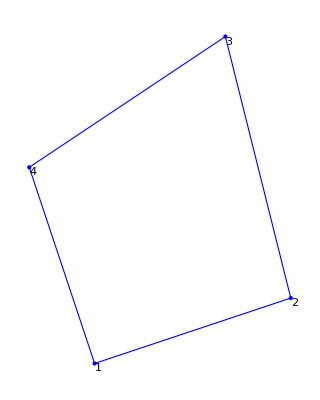

Length[nnodes] = 4

nels rows= 4

(0.407005 | 0.104972 | -0.300742 | -0.139621 | -0.0902343 | -0.115496 | -0.0160288 | 0.150145
0.104972 | 0.545515 | -0.0729543 | -0.0286192 | -0.115496 | -0.277013 | 0.0834783 | -0.239883
-0.300742 | -0.0729543 | 0.702964 | -0.142679 | 0.0518507 | 0.0812231 | -0.454073 | 0.13441
-0.139621 | -0.0286192 | -0.142679 | 0.393915 | 0.14789 | -0.182347 | 0.13441 | -0.182949
-0.0902343 | -0.115496 | 0.0518507 | 0.14789 | 0.316499 | 0.107979 | -0.278116 | -0.140373
-0.115496 | -0.277013 | 0.0812231 | -0.182347 | 0.107979 | 0.4688 | -0.073706 | -0.00944048
-0.0160288 | 0.0834783 | -0.454073 | 0.13441 | -0.278116 | -0.073706 | 0.748217 | -0.144182
0.150145 | -0.239883 | 0.13441 | -0.182949 | -0.140373 | -0.00944048 | -0.144182 | 0.432273)

```mathematica
order=1;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{2,1},{5,2},{4,6},{1,4}}}
topol={{1,2,3,4}}
eltype=1;
forcing=0.;
nnodes={{2,1},{5,2},{4,6},{1,4}};
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis]
{kE,fE}=Assemble[allcoords,topol,order,forcing,eltype];
MatrixForm[kE]
```

{{{0,0},{0.5,0.5},{0.3,1}}}

{{1,2,3}}

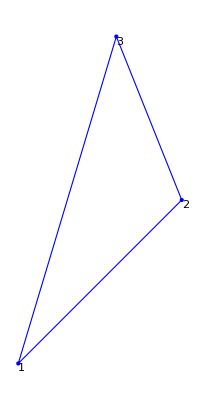

Length[nnodes] = 3

nels rows= 3

(0.40381 | 0.0952381 | -0.727619 | -0.0571429 | 0.32381 | -0.0380952
0.0952381 | 0.20381 | 0.00952381 | -0.194286 | -0.104762 | -0.00952381
-0.727619 | 0.00952381 | 1.57524 | -0.285714 | -0.847619 | 0.27619
-0.0571429 | -0.194286 | -0.285714 | 0.708571 | 0.342857 | -0.514286
0.32381 | -0.104762 | -0.847619 | 0.342857 | 0.52381 | -0.238095
-0.0380952 | -0.00952381 | 0.27619 | -0.514286 | -0.238095 | 0.52381)

```mathematica
order=1;
young=1;
nu=0.25;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{0.5,0.5},{0.3,1}}}
topol={{1,2,3}}
eltype=2;
forcing=0.;
nnodes={{0,0},{0.5,0.5},{0.3,1}};
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis]
{kE,fE}=Assemble[allcoords,topol,order,forcing,eltype];
MatrixForm[kE]
```

{{{0,0},{10,0},{0,6}},{{10,0},{10,6},{0,6}}}

{{1,2,3},{2,4,3}}

{{0,0},{10,0},{0,6},{10,6}}

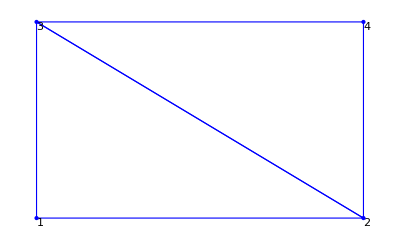

Length[nnodes] = 4

nels rows= 6

(6.50183×10^18 | 3.57143×10^6 | -3.2967×10^6 | -1.92308×10^6 | -3.20513×10^6 | -1.64835×10^6 | 0 | 0
3.57143×10^6 | 1.03114×10^19 | -1.64835×10^6 | -1.15385×10^6 | -1.92308×10^6 | -9.15751×10^6 | 0 | 0
-3.2967×10^6 | -1.64835×10^6 | 6.50183×10^6 | 0. | 0. | 3.57143×10^6 | -3.20513×10^6 | -1.92308×10^6
-1.92308×10^6 | -1.15385×10^6 | 0. | 1.03114×10^19 | 3.57143×10^6 | 0. | -1.64835×10^6 | -9.15751×10^6
-3.20513×10^6 | -1.92308×10^6 | 0. | 3.57143×10^6 | 6.50183×10^18 | 0. | -3.2967×10^6 | -1.64835×10^6
-1.64835×10^6 | -9.15751×10^6 | 3.57143×10^6 | 0. | 0. | 1.03114×10^7 | -1.92308×10^6 | -1.15385×10^6
0 | 0 | -3.20513×10^6 | -1.64835×10^6 | -3.2967×10^6 | -1.92308×10^6 | 6.50183×10^6 | 3.57143×10^6
0 | 0 | -1.92308×10^6 | -9.15751×10^6 | -1.64835×10^6 | -1.15385×10^6 | 3.57143×10^6 | 1.03114×10^7)

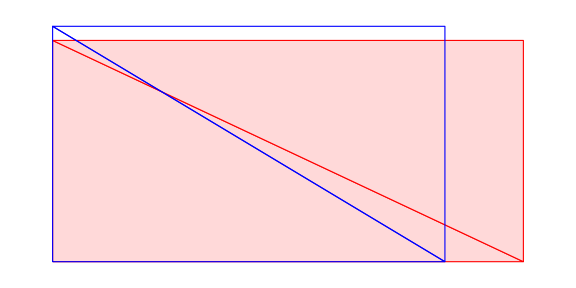

```mathematica
order=1;
young=10 10^6;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
allcoords={{{0,0},{10,0},{0,6}},{{10,0},{10,6},{0,6}}}
topol={{1,2,3},{2,4,3}}
eltype=2;
forcing=0.;
nnodes={{0,0},{10,0},{0,6},{10,6}}
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis]
{KE,FE}=Assemble[allcoords,topol,order,forcing,eltype];
{KE,FE}=ApplyNodeBC[KE,FE,1,0,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,2,0,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,3,0,{{10^12,1},{1,1}},{0,0}];
{KE,FE}=ApplyNodeBC[KE,FE,2,1,{{1,1},{1,1}},{6000,0}];
{KE,FE}=ApplyNodeBC[KE,FE,4,1,{{1,1},{1,1}},{6000,0}];
MatrixForm[KE]
sol=LinearSolve[KE,FE,Method->"Banded"];
scale=1000;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3}]]]]}];
Show[meshVisDef,meshVis1,ImageSize->Large]
```

```mathematica
sol//Chop
```

{0,0,0.002,0,0,-0.00036,0.002,-0.00036}

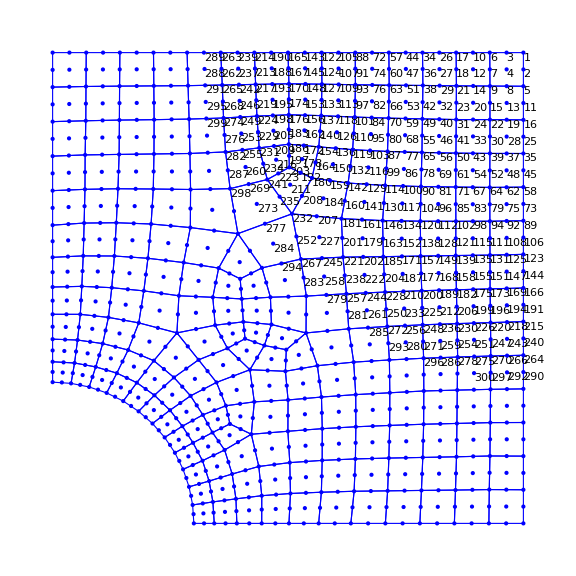

Length[nnodes] = 871

nels rows= 1818

-Graphics-

Possivel BUG!, Modificar rangesearch para o tamanho de elemento em uso!

rangesearch = 10.

5998.93

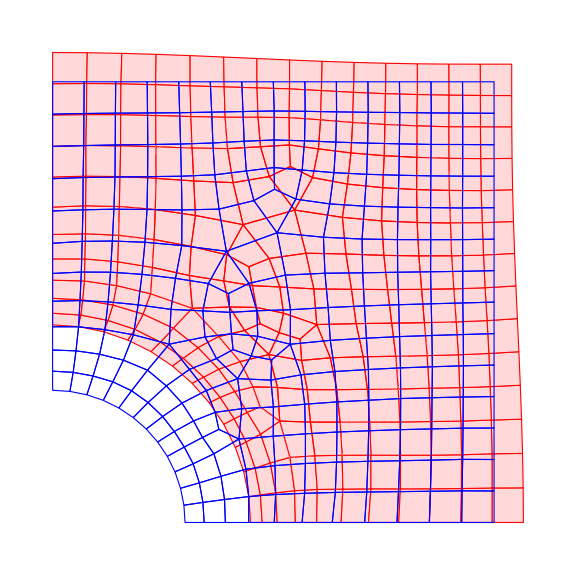

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\elschapacomfuroleft.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\noschapacomfuroleft.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,9}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis,ImageSize->Large]
order=2;
forcing=0.;
young=210000;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
eltype=1;
{KE,FE}=Assemble[allcoords,topol,order,forcing,eltype];
MatrixPlot[KE,ImageSize->Large]
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,870,644,{{1,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,871,645,{{10^12,1},{1,1}},{0,0}];
tol=10^-4;
radius=300;
radiusdir=3;
coordy=0;(*naoprecisa*)
{newnodes,vecids}=ComputeBoundaryTopol[radiusdir,coordy,radius,nnodes,tol,order];
FE=Table[0,{Length[KE]}];
f[x_]:=10;
order=2;
FE=ContributeLineNewmanCurverd[FE,f,order,newnodes,vecids];
Sum[FE[[i]],{i,1,Length[FE]}]
sol=LinearSolve[KE,FE,Method->"Banded"];
scale=7000;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];
Show[meshVisDef,meshVis1,ImageSize->Large]
```

```mathematica
{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol,eltype]//Simplify//Chop;
stress=ComputeStress[(dsols),210000.,0.30][[1]]//Simplify//Chop;
```

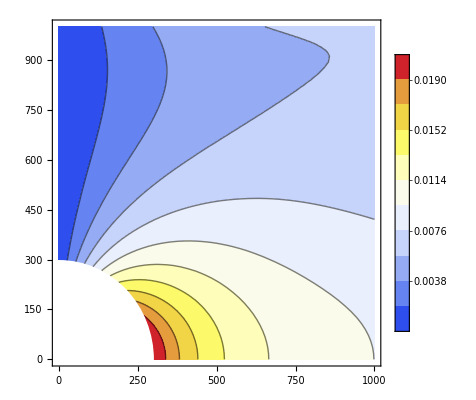

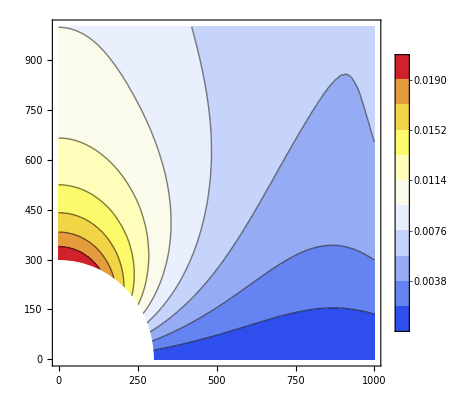

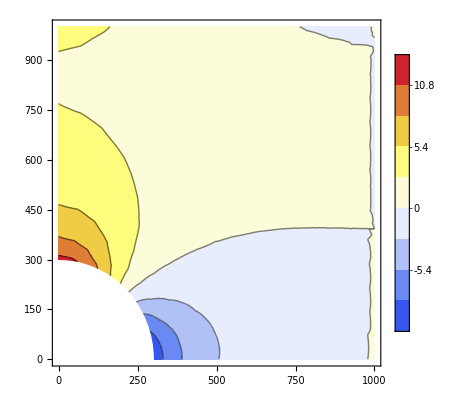

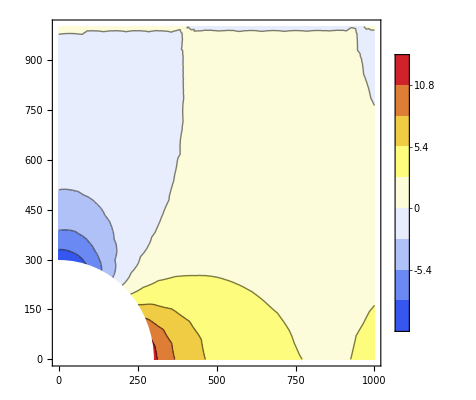

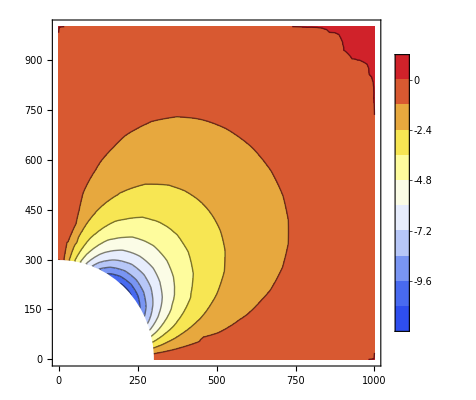

```mathematica
sollists={};
sx=1;
refine=0.5;
v=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->Automatic];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 
sollists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->Automatic];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 


stresslists={};
sx=1;

For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->{-15,15}];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 

stresslists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10,PlotRange->{-15,15}];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd] 

stresslists={};
sx=3;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->10 ,PlotRange->{-12,2}];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},300]},AspectRatio->Automatic]];
Show[lp,lpd]
```

```mathematica
tol=10^-4;
radius=0.;
ydir=2;
coordy=8;
{newnodes,vecids}=ComputeBoundaryTopol[ydir,coordy,radius,nnodes,tol,1]
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

{{},{}}

```mathematica
vecids={{223,242},{242,264},{264,285},{285,306},{306,344},{344,455},{455,498},{498,529},{529,553},{553,579},{579,608}}
newnodes={{{5.,8.},{5.3,8.}},{{5.3,8.},{5.6,8.}},{{5.6,8.},{5.9,8.}},{{5.9,8.},{6.2,8.}},{{6.2,8.},{6.5,8.}},{{6.5,8.},{6.8,8.}},{{6.8,8.},{7.1,8.}},{{7.1,8.},{7.4,8.}},{{7.4,8.},{7.7,8.}},{{7.7,8.},{8.,8.}}}
```

{{223,242},{242,264},{264,285},{285,306},{306,344},{344,455},{455,498},{498,529},{529,553},{553,579},{579,608}}

{{{5.,8.},{5.3,8.}},{{5.3,8.},{5.6,8.}},{{5.6,8.},{5.9,8.}},{{5.9,8.},{6.2,8.}},{{6.2,8.},{6.5,8.}},{{6.5,8.},{6.8,8.}},{{6.8,8.},{7.1,8.}},{{7.1,8.},{7.4,8.}},{{7.4,8.},{7.7,8.}},{{7.7,8.},{8.,8.}}}

```mathematica
Length[vecids]
Length[newnodes]
```

11

10

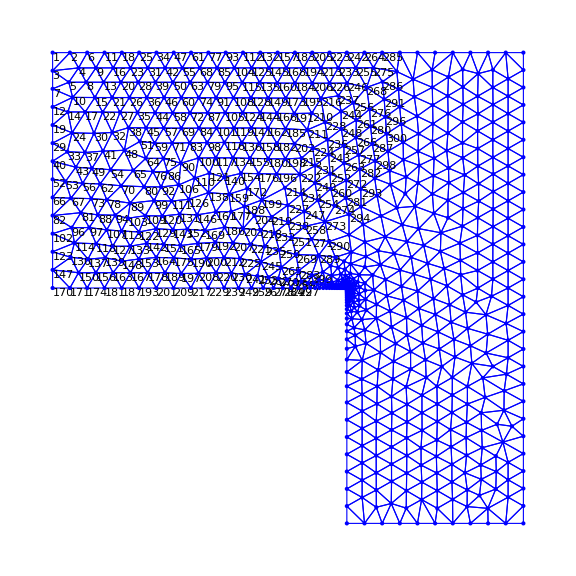

Length[nnodes] = 768

nels rows= 4155

-Graphics-

{{242,264},{264,285},{285,306},{306,344},{344,455},{455,498},{498,529},{529,553},{553,579},{579,608}}

{{{5.,8.},{5.3,8.}},{{5.3,8.},{5.6,8.}},{{5.6,8.},{5.9,8.}},{{5.9,8.},{6.2,8.}},{{6.2,8.},{6.5,8.}},{{6.5,8.},{6.8,8.}},{{6.8,8.},{7.1,8.}},{{7.1,8.},{7.4,8.}},{{7.4,8.},{7.7,8.}},{{7.7,8.},{8.,8.}}}

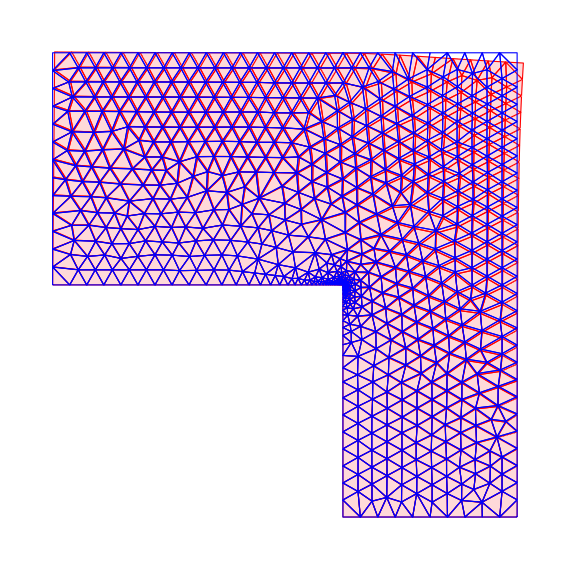

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\elstrip1.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\nodestrip1.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,3}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis,ImageSize->Large]
order=1;
forcing=0.;
young=3 10^7;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
eltype=2;
{KE,FE}=Assemble[allcoords,topol,order,forcing,eltype];
MatrixPlot[KE,ImageSize->Large]
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,170,406,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,710,406,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,710,768,{{10^12,1},{1,10^12}},{0,0}];

vecids={{242,264},{264,285},{285,306},{306,344},{344,455},{455,498},{498,529},{529,553},{553,579},{579,608}}
newnodes={{{5.,8.},{5.3,8.}},{{5.3,8.},{5.6,8.}},{{5.6,8.},{5.9,8.}},{{5.9,8.},{6.2,8.}},{{6.2,8.},{6.5,8.}},{{6.5,8.},{6.8,8.}},{{6.8,8.},{7.1,8.}},{{7.1,8.},{7.4,8.}},{{7.4,8.},{7.7,8.}},{{7.7,8.},{8.,8.}}}
c=3;
po=200;
f[x_]:=po Sin[Pi x/(2 c)];
FE=ContributeLineNewman[FE,f,order,newnodes,vecids];
Sum[FE[[i]],{i,1,Length[FE]}];
sol=LinearSolve[KE,FE,Method->"Banded"];

scale=7500;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3}]]]]}];
Show[meshVisDef,meshVis1,ImageSize->Large]
```

```mathematica
Symmetric
```

Symmetric

```mathematica
Max[sol]
Min[sol]
```

0.000014387

-0.0000235663

{{-68.8836,-229.612,52.7846},{93.1488,27.9446,-141.517},{-54.5499,-181.833,38.8254},{2.62151,-331.388,-6.6112},{-21.4365,-192.915,28.7837},{-18.241,-183.902,30.3197},1373,{0.033317,-3.03116,11.2931},{3.00509,-1.77197,11.0011},{1.35819,1.36353,12.7223},{-0.0670458,2.67824,0.838399},{-2.71572,-21.2924,-4.17676},{31.3446,-21.1516,-11.7737}}
 |  |  |  |

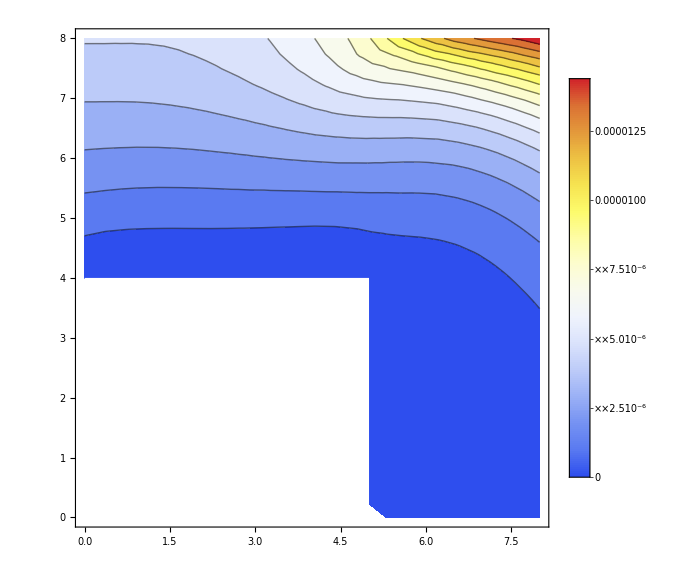

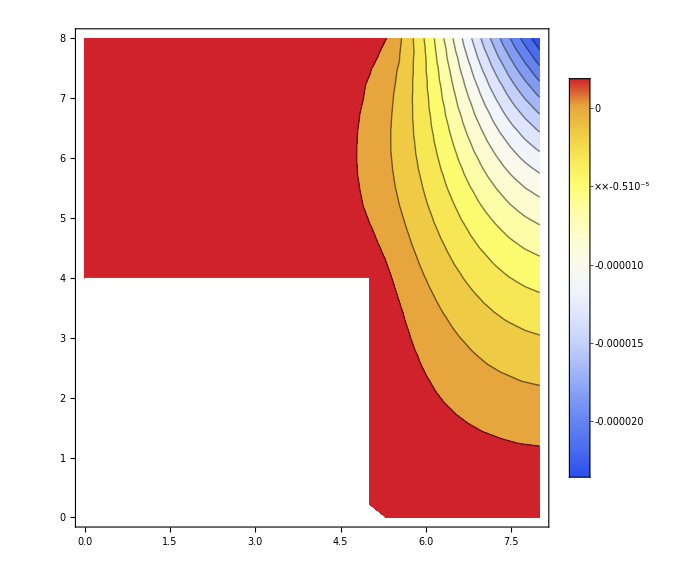

```mathematica
{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol,eltype]//Simplify//Chop;
stress=ComputeStress[(dsols),young,nu][[1]]//Simplify//Chop
Clear[x,y,Sol];
sollists={};
sx=1;
refine=1/3.;
v=Table[{xi,eta},{xi,0,1,refine},{eta,0,1-xi,refine}];
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->Large];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
sollists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->Large];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]

(*stresslists={};
sx=1;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]];
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],stress[[i,sx]]},{i,1,Length[x]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->Automatic,ImageSize->Large];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
stresslists={};
sx=2;
For[i=j,j≤Length[stress],j++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->Automatic,ImageSize->Large];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
stresslists={};
sx=3;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->Automatic,ImageSize->Large];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]*)
```

```mathematica
tol=10^-4;
radius=0.;
ydir=2;
coordy=8;
{newnodes,vecids}=ComputeBoundaryTopol[ydir,coordy,radius,nnodes,tol,2]
```

{{{{0.,8.},{0.294118,8.},{0.588235,8.}},{{0.588235,8.},{0.882353,8.},{1.17647,8.}},{{1.17647,8.},{1.47059,8.},{1.76471,8.}},{{1.76471,8.},{2.05882,8.},{2.35294,8.}},{{2.35294,8.},{2.64706,8.},{2.94118,8.}},{{2.94118,8.},{3.23529,8.},{3.52941,8.}},{{3.52941,8.},{3.82353,8.},{4.11765,8.}},{{4.11765,8.},{4.41176,8.},{4.70588,8.}},{{4.70588,8.},{5.,8.},{5.3,8.}},{{5.3,8.},{5.6,8.},{5.9,8.}},{{5.9,8.},{6.2,8.},{6.5,8.}},{{6.5,8.},{6.8,8.},{7.1,8.}},{{7.1,8.},{7.4,8.},{7.7,8.}}},{{1,2,6},{6,11,18},{18,25,34},{34,47,61},{61,77,93},{93,112,132},{132,157,183},{183,205,223},{223,242,264},{264,285,306},{306,344,455},{455,498,529},{529,553,579}}}

```mathematica
vecids={{927,969,1005},{1005,1048,1088},{1088,1130,1177},{1177,1239,1314},{1314,1453,1728},{1728,1834,1901},{1901,1957,2011},{2011,2062,2112},{2112,2161,2214},{2214,2268,2323}}
newnodes={{{5.,8.},{5.15,8.},{5.3,8.}},{{5.3,8.},{5.45,8.},{5.6,8.}},{{5.6,8.},{5.75,8.},{5.9,8.}},{{5.9,8.},{6.05,8.},{6.2,8.}},{{6.2,8.},{6.35,8.},{6.5,8.}},{{6.5,8.},{6.65,8.},{6.8,8.}},{{6.8,8.},{6.95,8.},{7.1,8.}},{{7.1,8.},{7.25,8.},{7.4,8.}},{{7.4,8.},{7.55,8.},{7.7,8.}},{{7.7,8.},{7.85,8.},{8.,8.}}}
```

{{927,969,1005},{1005,1048,1088},{1088,1130,1177},{1177,1239,1314},{1314,1453,1728},{1728,1834,1901},{1901,1957,2011},{2011,2062,2112},{2112,2161,2214},{2214,2268,2323}}

{{{5.,8.},{5.15,8.},{5.3,8.}},{{5.3,8.},{5.45,8.},{5.6,8.}},{{5.6,8.},{5.75,8.},{5.9,8.}},{{5.9,8.},{6.05,8.},{6.2,8.}},{{6.2,8.},{6.35,8.},{6.5,8.}},{{6.5,8.},{6.65,8.},{6.8,8.}},{{6.8,8.},{6.95,8.},{7.1,8.}},{{7.1,8.},{7.25,8.},{7.4,8.}},{{7.4,8.},{7.55,8.},{7.7,8.}},{{7.7,8.},{7.85,8.},{8.,8.}}}

```mathematica
Length[vecids]
Length[newnodes]
```

10

10

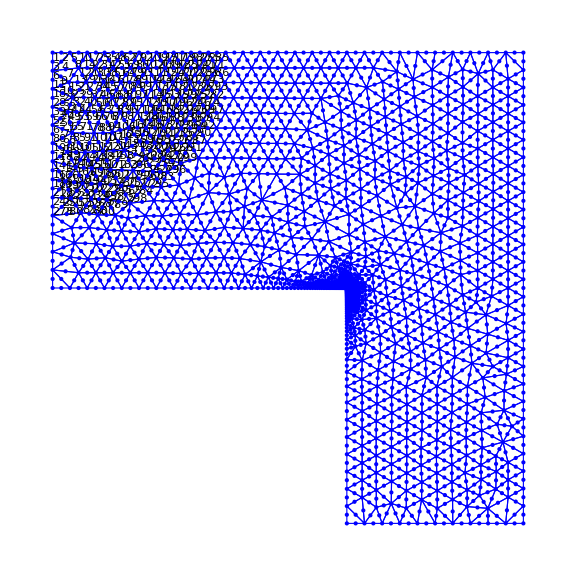

Length[nnodes] = 2920

nels rows= 8310

-Graphics-

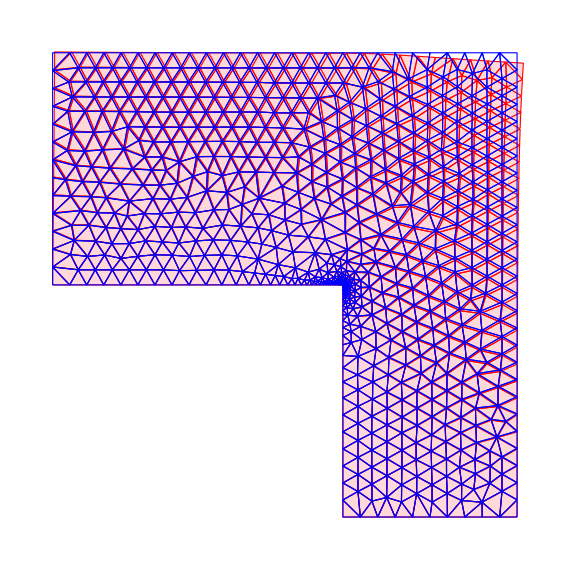

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\elsstrip2.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\nodestrip2.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,6}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis,ImageSize->Large]
order=2;
forcing=0.;
young=3 10^7;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
eltype=2;
{KE,FE}=Assemble[allcoords,topol,order,forcing,eltype];
MatrixPlot[KE,ImageSize->Large]
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,655,1552,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,2711,1552,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,2711,2920,{{10^12,1},{1,10^12}},{0,0}];

vecids={{927,969,1005},{1005,1048,1088},{1088,1130,1177},{1177,1239,1314},{1314,1453,1728},{1728,1834,1901},{1901,1957,2011},{2011,2062,2112},{2112,2161,2214},{2214,2268,2323}};
newnodes={{{5.,8.},{5.15,8.},{5.3,8.}},{{5.3,8.},{5.45,8.},{5.6,8.}},{{5.6,8.},{5.75,8.},{5.9,8.}},{{5.9,8.},{6.05,8.},{6.2,8.}},{{6.2,8.},{6.35,8.},{6.5,8.}},{{6.5,8.},{6.65,8.},{6.8,8.}},{{6.8,8.},{6.95,8.},{7.1,8.}},{{7.1,8.},{7.25,8.},{7.4,8.}},{{7.4,8.},{7.55,8.},{7.7,8.}},{{7.7,8.},{7.85,8.},{8.,8.}}};
c=3;
po=200;
f[x_]:=po Sin[Pi x/(2 c)];
FE=ContributeLineNewman[FE,f,order,newnodes,vecids];
Sum[FE[[i]],{i,1,Length[FE]}];
sol=LinearSolve[KE,FE,Method->"Banded"];

scale=7500;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3}]]]]}];
Show[meshVisDef,meshVis1,ImageSize->Large]
```

```mathematica
Max[sol]
Min[sol]
```

0.0000145146

-0.0000238398

```mathematica
(*{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol,eltype]//Simplify//Chop;
stress=ComputeStress[(dsols),young,nu][[1]]//Simplify//Chop*)
```

```mathematica
(*Clear[x,y,Sol];
sollists={};
sx=1;
refine=1/3.;
v=Table[{xi,eta},{xi,0,1,refine},{eta,0,1-xi,refine}];
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->Large];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
sollists={};
sx=2;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[sollists,sollist];

];
lp=ListContourPlot[Flatten[sollists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->All,ImageSize->Large];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]

stresslists={};
sx=1;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]];
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],stress[[i,sx]]},{i,1,Length[x]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->Automatic,ImageSize->Large];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
stresslists={};
sx=2;
For[i=1,j≤Length[stress],j++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->Automatic,ImageSize->Large];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]
stresslists={};
sx=3;
For[i=1,i≤Length[stress],i++,
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Stress[xii_,etaa_]:=stress[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Stress[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
stresslist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
AppendTo[stresslists,stresslist];

];
lp=ListContourPlot[Flatten[stresslists,1],ColorFunction->"TemperatureMap",AspectRatio->Automatic,PlotLegends->Automatic,Contours->15,PlotRange->Automatic,ImageSize->Large];
lpd=Show[Graphics[{GrayLevel[1],Rectangle[{0,0},{5,4}]},AspectRatio->Automatic]];
Show[lp,lpd]*)
```

```mathematica
tol=10^-4;
radius=0.;
ydir=2;
coordy=8;
{newnodes,vecids}=ComputeBoundaryTopol[ydir,coordy,radius,nnodes,tol,1]
```

{{{{0.,8.},{0.147059,8.}},{{0.147059,8.},{0.294118,8.}},{{0.294118,8.},{0.441176,8.}},{{0.441176,8.},{0.588235,8.}},{{0.588235,8.},{0.735294,8.}},{{0.735294,8.},{0.882353,8.}},{{0.882353,8.},{1.02941,8.}},{{1.02941,8.},{1.17647,8.}},{{1.17647,8.},{1.32353,8.}},{{1.32353,8.},{1.47059,8.}},{{1.47059,8.},{1.61765,8.}},{{1.61765,8.},{1.76471,8.}},{{1.76471,8.},{1.91176,8.}},{{1.91176,8.},{2.05882,8.}},{{2.05882,8.},{2.20588,8.}},{{2.20588,8.},{2.35294,8.}},{{2.35294,8.},{2.5,8.}},{{2.5,8.},{2.64706,8.}},{{2.64706,8.},{2.79412,8.}},{{2.79412,8.},{2.94118,8.}},{{2.94118,8.},{3.08824,8.}},{{3.08824,8.},{3.23529,8.}},{{3.23529,8.},{3.38235,8.}},{{3.38235,8.},{3.52941,8.}},{{3.52941,8.},{3.67647,8.}},{{3.67647,8.},{3.82353,8.}},{{3.82353,8.},{3.97059,8.}},{{3.97059,8.},{4.11765,8.}},{{4.11765,8.},{4.26471,8.}},{{4.26471,8.},{4.41176,8.}},{{4.41176,8.},{4.55882,8.}},{{4.55882,8.},{4.70588,8.}},{{4.70588,8.},{4.85294,8.}},{{4.85294,8.},{5.,8.}},{{5.,8.},{5.15,8.}},{{5.15,8.},{5.3,8.}},{{5.3,8.},{5.45,8.}},{{5.45,8.},{5.6,8.}},{{5.6,8.},{5.75,8.}},{{5.75,8.},{5.9,8.}},{{5.9,8.},{6.05,8.}},{{6.05,8.},{6.2,8.}},{{6.2,8.},{6.35,8.}},{{6.35,8.},{6.5,8.}},{{6.5,8.},{6.65,8.}},{{6.65,8.},{6.8,8.}},{{6.8,8.},{6.95,8.}},{{6.95,8.},{7.1,8.}},{{7.1,8.},{7.25,8.}},{{7.25,8.},{7.4,8.}},{{7.4,8.},{7.55,8.}},{{7.55,8.},{7.7,8.}},{{7.7,8.},{7.85,8.}},{{7.85,8.},{8.,8.}}},{{1,2},{2,5},{5,10},{10,17},{17,25},{25,35},{35,48},{48,62},{62,77},{77,92},{92,109},{109,127},{127,151},{151,173},{173,198},{198,227},{227,255},{255,285},{285,316},{316,350},{350,387},{387,425},{425,463},{463,506},{506,551},{551,597},{597,645},{645,695},{695,736},{736,776},{776,814},{814,851},{851,887},{887,927},{927,969},{969,1005},{1005,1048},{1048,1088},{1088,1130},{1130,1177},{1177,1239},{1239,1314},{1314,1453},{1453,1728},{1728,1834},{1834,1901},{1901,1957},{1957,2011},{2011,2062},{2062,2112},{2112,2161},{2161,2214},{2214,2268},{2268,2323}}}

```mathematica
newnodes={{{5.,8.},{5.3,8.}},{{5.3,8.},{5.6,8.}},{{5.6,8.},{5.9,8.}},{{5.9,8.},{6.2,8.}},{{6.2,8.},{6.5,8.}},{{6.5,8.},{6.8,8.}},{{6.8,8.},{7.1,8.}},{{7.1,8.},{7.4,8.}},{{7.4,8.},{7.7,8.}},{{7.7,8.},{8.,8.}}};
vecids={{225,243},{243,262},{262,290},{290,332},{332,488},{488,543},{543,575},{575,601},{601,623},{623,653}};
Length[newnodes]
Length[vecids]
```

10

10

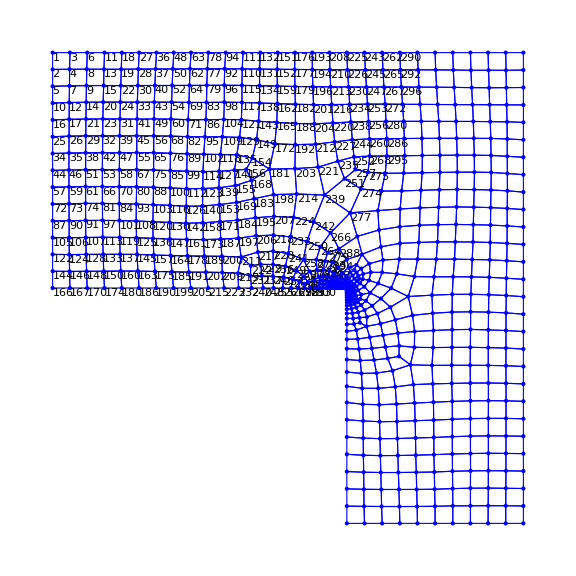

Length[nnodes] = 797

nels rows= 2884

-Graphics-

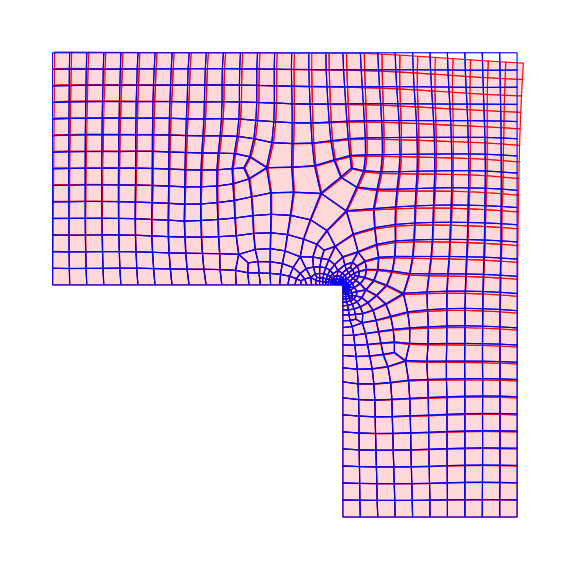

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\quadp1Lshapeels.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\quadp1Lshapenode.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,4}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis,ImageSize->Large]
order=1;
forcing=0.;
young=3 10^7;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
eltype=1;
{KE,FE}=Assemble[allcoords,topol,order,forcing,eltype];
MatrixPlot[KE,ImageSize->Large]
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,166,427,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,743,427,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,743,797,{{10^12,1},{1,10^12}},{0,0}];

newnodes={{{5.,8.},{5.3,8.}},{{5.3,8.},{5.6,8.}},{{5.6,8.},{5.9,8.}},{{5.9,8.},{6.2,8.}},{{6.2,8.},{6.5,8.}},{{6.5,8.},{6.8,8.}},{{6.8,8.},{7.1,8.}},{{7.1,8.},{7.4,8.}},{{7.4,8.},{7.7,8.}},{{7.7,8.},{8.,8.}}};
vecids={{225,243},{243,262},{262,290},{290,332},{332,488},{488,543},{543,575},{575,601},{601,623},{623,653}};
c=3;
po=200;
f[x_]:=po Sin[Pi x/(2 c)];
FE=ContributeLineNewman[FE,f,order,newnodes,vecids];
Sum[FE[[i]],{i,1,Length[FE]}];
sol=LinearSolve[KE,FE,Method->"Banded"];

scale=7500;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];
Show[meshVisDef,meshVis1,ImageSize->Large]
```

```mathematica
Max[sol]
Min[sol]
```

0.0000144684

-0.0000237478

```mathematica
newnodes={{{5.,8.},{5.15,8.},{5.3,8.}},{{5.3,8.},{5.45,8.},{5.6,8.}},{{5.6,8.},{5.75,8.},{5.9,8.}},{{5.9,8.},{6.05,8.},{6.2,8.}},{{6.2,8.},{6.35,8.},{6.5,8.}},{{6.5,8.},{6.65,8.},{6.8,8.}},{{6.8,8.},{6.95,8.},{7.1,8.}},{{7.1,8.},{7.25,8.},{7.4,8.}},{{7.4,8.},{7.55,8.},{7.7,8.}},{{7.7,8.},{7.85,8.},{8.,8.}}};
vecids={{858,891,926},{926,960,1001},{1001,1049,1106},{1106,1174,1269},{1269,1450,1856},{1856,1988,2075},{2075,2140,2196},{2196,2246,2297},{2297,2339,2394},{2394,2445,2500}};
Length[newnodes]
Length[vecids]
```

10

10

```mathematica
tol=10^-4;
radius=0.;
ydir=2;
coordy=8;
{newnodes,vecids}=ComputeBoundaryTopol[ydir,coordy,radius,nnodes,tol,2]
```

{{{{0.,8.},{0.294118,8.},{0.588235,8.}},{{0.588235,8.},{0.882353,8.},{1.17647,8.}},{{1.17647,8.},{1.47059,8.},{1.76471,8.}},{{1.76471,8.},{2.05882,8.},{2.35294,8.}},{{2.35294,8.},{2.64706,8.},{2.94118,8.}},{{2.94118,8.},{3.23529,8.},{3.52941,8.}},{{3.52941,8.},{3.82353,8.},{4.11765,8.}},{{4.11765,8.},{4.41176,8.},{4.70588,8.}},{{4.70588,8.},{5.,8.},{5.3,8.}},{{5.3,8.},{5.6,8.},{5.9,8.}},{{5.9,8.},{6.2,8.},{6.5,8.}},{{6.5,8.},{6.8,8.},{7.1,8.}},{{7.1,8.},{7.4,8.},{7.7,8.}}},{{1,3,6},{6,11,18},{18,27,36},{36,48,63},{63,78,94},{94,111,132},{132,151,176},{176,193,208},{208,225,243},{243,262,290},{290,332,488},{488,543,575},{575,601,623}}}

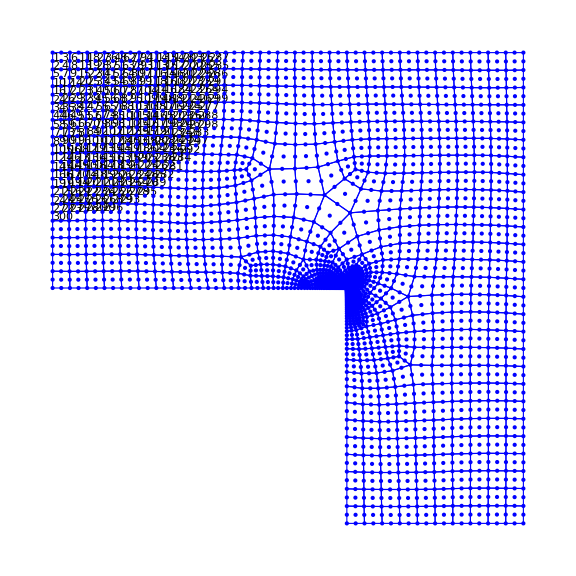

Length[nnodes] = 3035

nels rows= 6489

-Graphics-

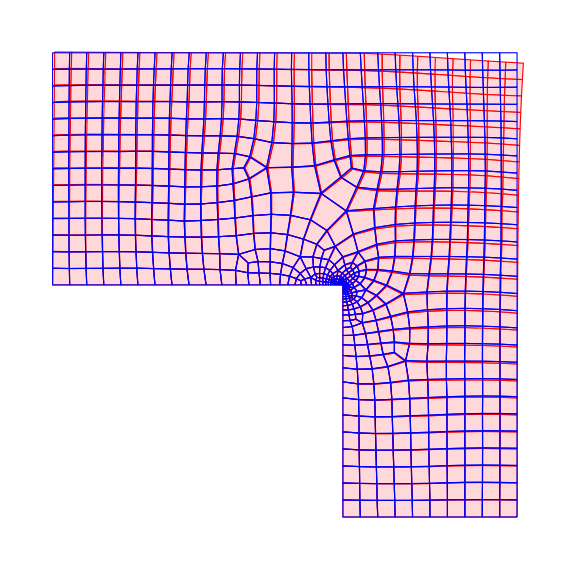

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\quadp2Lshapeels.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\mathematica\\mathematica\\quadp2Lshapenode.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,9}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,2,3,4}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
Show[meshVis1,nodeVis,ImageSize->Large]
order=2;
forcing=0.;
young=3 10^7;
nu=0.3;
mu=young/(2(1+nu));
lambda=young nu/((1+nu)(1-2nu));
eltype=1;
{KE,FE}=Assemble[allcoords,topol,order,forcing,eltype];
MatrixPlot[KE,ImageSize->Large]
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,637,1634,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,2843,1634,{{10^12,1},{1,10^12}},{0,0}];
{KE,FE}=ContributeLineDirichlet[KE,FE,nnodes,2843,3035,{{10^12,1},{1,10^12}},{0,0}];

newnodes={{{5.,8.},{5.15,8.},{5.3,8.}},{{5.3,8.},{5.45,8.},{5.6,8.}},{{5.6,8.},{5.75,8.},{5.9,8.}},{{5.9,8.},{6.05,8.},{6.2,8.}},{{6.2,8.},{6.35,8.},{6.5,8.}},{{6.5,8.},{6.65,8.},{6.8,8.}},{{6.8,8.},{6.95,8.},{7.1,8.}},{{7.1,8.},{7.25,8.},{7.4,8.}},{{7.4,8.},{7.55,8.},{7.7,8.}},{{7.7,8.},{7.85,8.},{8.,8.}}};
vecids={{858,891,926},{926,960,1001},{1001,1049,1106},{1106,1174,1269},{1269,1450,1856},{1856,1988,2075},{2075,2140,2196},{2196,2246,2297},{2297,2339,2394},{2394,2445,2500}};
c=3;
po=200;
f[x_]:=po Sin[Pi x/(2 c)];
FE=ContributeLineNewman[FE,f,order,newnodes,vecids];
Sum[FE[[i]],{i,1,Length[FE]}];
sol=LinearSolve[KE,FE,Method->"Banded"];

scale=7500;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVisDef=Graphics[{FaceForm[{LightRed,Opacity[3]}],EdgeForm[Red],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,2,3,4}]]]]}];
Show[meshVisDef,meshVis1,ImageSize->Large]
```

```mathematica
Max[sol]
Min[sol]
```

0.000014516

-0.0000238379